```mathematica
Import[NotebookDirectory[]<>"ExplicitThinPlateElasticitylib.m"];(*load the functions*)
```

```mathematica
(*Plot the deflection (u) of the points in 2D (coord)*)
MyPlotPoint[coord_List,u_List,plotRange_:Automatic]:=Module[{Nnode=Length[coord],ndim=Length[coord[[1]]],xyz={},uv={"u","v","w"},r,r2},
If[Length[coord]>Length[u],Print["Error,u is less than coord"];Abort[]];xyz=ConstantArray[0.,{Nnode,ndim+1}];xyz[[All,1;;ndim]]=coord;
If[Length[u]==Nnode,xyz[[All,ndim+1]]=u;CellPrint@ExpressionCell[#,"Output"]&/@{ListPointPlot3D[xyz,PlotLegends->Automatic, Axes->True,AxesLabel->{"x","y"},PlotLabel->"u",PlotRange->plotRange, ColorFunction->"SouthwestColors"]},
Do[xyz[[All,ndim+1]]=u[[iu;;-1;;ndim]];
CellPrint@ExpressionCell[#,"Output"]&/@{ListPointPlot3D[xyz,PlotLegends->Automatic,Axes->True,AxesLabel->{"x","y"},PlotLabel->uv⟦iu⟧, ColorFunction->"Rainbow"]},{iu,ndim}]]];
MyPlotPoint[coord_List,u_List,pset_List,plotRange_:Automatic]:=Module[{Nnode=Length[coord],ndim=Length[coord[[1]]],xyz={},uv={"u","v","w"},r,r2},
If[Length[coord]>Length[u],Print["Error,u is less than coord"];Abort[]];xyz=ConstantArray[0.,{Nnode,ndim+1}];xyz[[All,1;;ndim]]=coord;
If[Length[u]==Nnode,xyz[[All,ndim+1]]=u;CellPrint@ExpressionCell[#,"Output"]&/@{ListPointPlot3D[xyz[[pset,All]],PlotLegends->Automatic, Axes->True,AxesLabel->{"x","y"},PlotLabel->"u",PlotRange->plotRange, ColorFunction->"SouthwestColors"]},
Do[xyz[[All,ndim+1]]=u[[iu;;-1;;ndim]];
CellPrint@ExpressionCell[#,"Output"]&/@{ListPointPlot3D[xyz[[pset]],PlotLegends->Automatic,Axes->True,AxesLabel->{"x","y"},PlotLabel->uv⟦iu⟧, ColorFunction->"Rainbow"]},{iu,ndim}]]];
```

## Models

All elements are in good condition

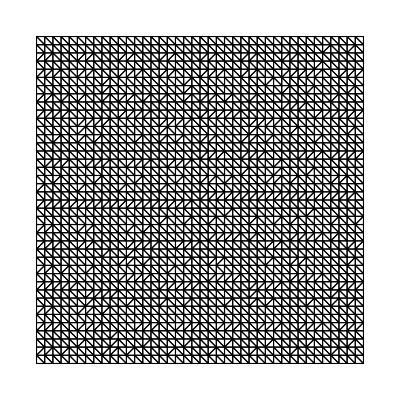

```mathematica
L=0.5;H=0.5;thickness0=0.01;udim=1;
(*In thin plate model, udim=1 means that deflection is scalar-valued based. The global dof index is the same as the particle index. *)
ndim=2;dx=L/40;
coord=N[GridNdim[{0,0},{L, H},dx]];
Nnode=Length[coord];
ndof=Nnode udim;
uvw=ConstantArray[0.,{Nnode,udim}];
pvol=L*H/Nnode;
nExt=10orderDeri;
numNei=numDeri+nExt;(*number of neighbors in the support. The scheme of NOM uses fixed number of neighbors for each particle, rather than the support size.*)
Nei=nearestNeighbours[coord,numNei];(*construct the neighbors for each particle*)
pvol=ConstantArray[pvol,Nnode];(*particle volume*)
mesh1=MyDelaunayMesh[coord];
ShowMesh[mesh1]
```

```mathematica
WeiF=Wfr2;QuinticKer;(*weight function*)
np=-1;
hgPen=1.0;(*hourglass penalty*)
{PW,KHG}=NOMPwKhg[np,coord,pvol,Nei,pfun,WeiF,hgPen ];(*PW is similar to B matrix. KHG is the list of all operator energy matrix.*)
```

For selected nodes:{170,615,1229,712,665,936,60,238,625,1464}

Condition number of NOM:{7.20242,47.2928,11.942,7.20242,7.20242,7.20242,11.442,7.20242,7.20242,7.20242}

```mathematica
forceList=FindPoints[coord,{0,0}+0.1dx,{L,L}-0.1 dx];(*the particle indices to be applied with pressure load*)
fixList=Complement[Range[Nnode],forceList];(*the boundary particles to be fixed.*)
```

```mathematica
fixList//Length
```

160

```mathematica
fixListright//Length
```

369

```mathematica
pDirichlet=10.^6;
fixFun[xyz_List]:=ConstantArray[0.,udim];
fx=10.^6;forceFun[xyz_List]:={fx dx^2};
(*In thin plate model, udim=1 means that deflection is scalar-valued based. The global dof index is the same as the particle index. *)
fixValues=BCValuesFunc[fixList,coord,fixFun,udim];
forceValues=BCValuesFunc[forceList,coord,forceFun,udim];
dofFix=DofIndexValue[fixList,fixValues];(*fixList is the particle to be fixed, fixValues is the fixed value for each particle. fixValues should be a list of list, each sublist with length of udim.*)
dofForce=DofIndexValue[forceList,forceValues];
```

```mathematica
dofVelo={{},{}};
```

```mathematica
rindex=ParticleNeighDof[Nei,udim];
(*In thin plate model, udim=1 means that deflection is scalar-valued based. The global dof index is the same as the particle index. Here rindex is the same as the neighbor list. *)
```

```mathematica
AbortOnMessage[]
```

```mathematica
El0=210. 10^9;nu0=0.3;thickness0=thickness0;rho0=7850.;phg0=0El0;(*hourglass penalty is assumed to be zero for thin plate.*)
massMatrix=Flatten[Table[ConstantArray[thickness0 rho0 pvol[[i]],udim],{i,Length[pvol]}]];
veloSound=Sqrt[El0/rho0];tIncMax=dx/veloSound;
ctime=0.;
tInc=0.4tIncMax;
TotalTime=10 tInc;
```

```mathematica
udof=ConstantArray[0.,{ndof}];
vdof=ConstantArray[0.,{ndof}];
adof=ConstantArray[0.,{ndof}];
adofNew=adof;
```

```mathematica
weiNeiList=WeiNeiList[coord,WeiF,Nei];
```

```mathematica
AbortOnMessage[]
```

```mathematica
umaxList={};
vmaxList={};
amaxList={};
```

```mathematica
pcenter=FindPoints[coord,{L,L}0.5-0.2dx,{L,L}0.5+0.2dx][[1]]
```

841

```mathematica
pvol//Total
```

0.25

```mathematica
massMatrix//Total
```

19.625

```mathematica
0.25 rho0 thickness0
```

19.625

```mathematica
ClearAll[SaveToCell]
SaveToCell::usage="SaveToCell[variable] creates an input cell that reassigns the current value of variable.\n"<>"SaveToCell[variables, display] shows 'display' on the right-hand-side of the assignment.";
SetAttributes[SaveToCell,HoldFirst]
SaveToCell[var_,name:Except[_?OptionQ]:"data",opt:OptionsPattern[]]:=With[{data=Compress[var],panel=ToBoxes@Tooltip[Panel[name,FrameMargins->Small],DateString[]]},CellPrint@Cell[BoxData@RowBox[{MakeBoxes[var],"=",InterpretationBox[panel,Uncompress[data]],";"}],"Input",(*prevent deletion by Cell>Delete All Output:*)GeneratedCell->False,(*CellLabel is special:last occrrence takes precedence,so it comes before opt:*)CellLabel->"(saved)",opt,CellLabelAutoDelete->False]];
```

```mathematica
SaveStepList={500,1000,1500,2000,2500,3000,4000,5000,6000,7000};
```

```mathematica
outputInterval=50;j=1;
Do[udof+=tInc vdof+(0.5 tInc^2)adof;
udof[[dofFix[[1]]]]=dofFix[[2]];(*displacement constraint*)
AppendTo[umaxList,{ctime,udof[[pcenter]]}];
AppendTo[vmaxList,{ctime,vdof[[pcenter]]}];
AppendTo[amaxList,{ctime,adof[[pcenter]]}];
uvw=ArrayReshape[udof,{Nnode,udim}];
(*deriU=NOMPartialU0[uvw,PW,Nei];*)
(*deformList=FList[coord,coord0,NeiList,invKList,vol,WeiF];*)
(*internalF=ForceList[bulkK,shearG,coord,coord0,NeiList,deformList,invKList,trKList,WeiF,vol,penCoef];*)
internalF=-NOMResiPreValue3[Resi2,ndim,pvol,{El0,nu0,thickness0},uvw,PW,KHG,weiNeiList,Nei,rindex,phg0];(*-NOMResiPreValue2[Resi1,ndim,pvol,{El0,nu0,phg0},uvw,PW,KHG,Nei,rindex,phg0];*)
internalF[[dofForce[[1]]]]+=dofForce[[2]];(*add boundary forces to the internal force vector*)
adofNew=internalF/massMatrix;
vdof+=0.5 tInc (adof+adofNew);
If[MemberQ[SaveStepList,j],SaveToCell[{udof,vdof},"time:"<>ToString[ctime]]];
vdof[[dofVelo[[1]]]]=dofVelo[[2]];(*velocity constraint*)
adof=adofNew;
If[Mod[j,outputInterval]==1,Print["acc max:",Max[adofNew],",vel max:",Max[vdof],",umax: ",Max[udof]];
Print["step=",j,",t=",ctime," done"];];
ctime+=tInc;j++;
If[Mod[j,outputInterval]==1,Print[Plot2DField[uvw[[All,1]],mesh1]];(*Print[Plot2DField[uvw[[All,2]],mesh1]]*)]
,{i,9000}]
```

```mathematica
{0.97,2.9,4.83,6.77}
```

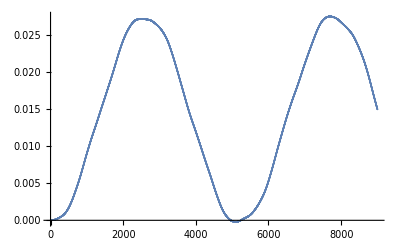

```mathematica
ListPlot[umaxList[[All,2]]]
```

```mathematica
{xtime,ytime,vtime,atime}="simple supported, 26x26, abaqus, s4r";
```

```mathematica
umaxList[[All,2]]//Max
```

0.0271473

```mathematica
SaveToCell[{umaxList,vmaxList},"simple support, nom, 40x40"]
```

```mathematica
{umaxList,vmaxList}="simple support, nom, 40x40";
```

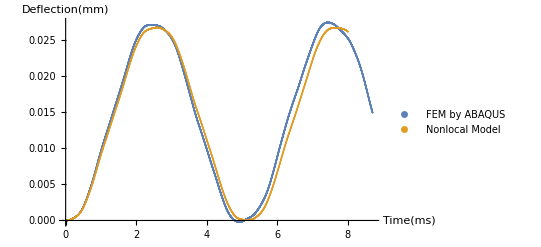

```mathematica
ListPlot[{{umaxList[[All,1]]*1000,umaxList[[All,2]]}ᵀ,{xtime,-ytime}ᵀ},PlotLegends->{"FEM by ABAQUS","Nonlocal Model"},AxesLabel->{HoldForm[Time[ms]],HoldForm[Deflection[mm]]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

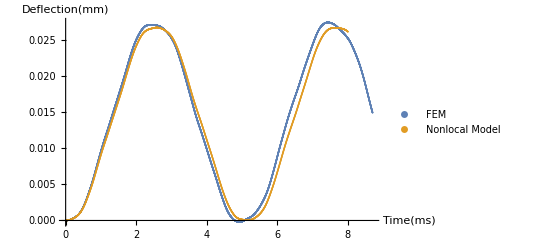

```mathematica
Show[%163,AxesLabel->{HoldForm[Time[ms]],HoldForm[Deflection[mm]]},PlotLabel->None,LabelStyle->{12,GrayLevel[0]}]
```

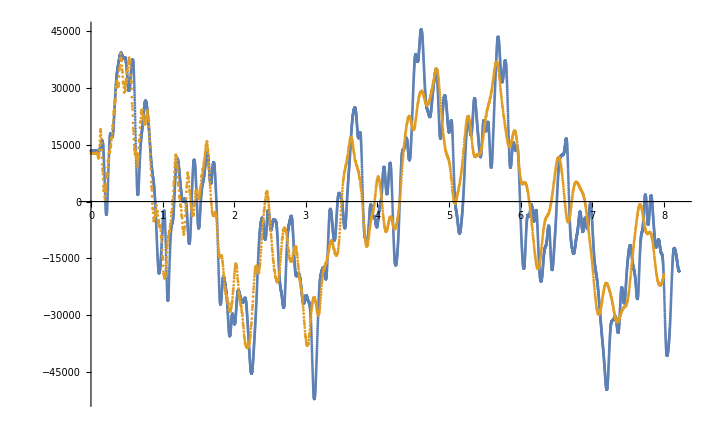

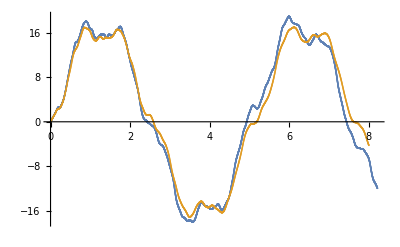

```mathematica
ListPlot[{{umaxList[[All,1]]*1000,amaxList[[All,2]]100}ᵀ,{xtime,-atime}ᵀ}]
ListPlot[{{umaxList[[All,1]]*1000,vmaxList[[All,2]]100}ᵀ,{xtime,-vtime}ᵀ}]
```

```mathematica
SaveToCell[coord,"simpled 40x40, coordinate"]
```

```mathematica
coord="simpled 40x40, coordinate";
```

```mathematica
(*{0.97,2.9,4.83,6.77} ms, s1,s3,s4,s7*)
MyPlotPoint[coord,10^-3udofs1]
MyPlotPoint[coord,10^-3udofs3]
MyPlotPoint[coord,10^-3udofs4]
MyPlotPoint[coord,10^-3udofs7]
```

-Graphics3D-

{Null}

-Graphics3D-

{Null}

-Graphics3D-

{Null}

-Graphics3D-